# Inflationary Era For Gauss-Bonnet Toy Models.

The present model is non-viable however the overall procedure is the same as in the previous file. The only difference is the scalar function that is freely designated. Now, the Gauss-Bonnet scalar coupling function is defined whereas the scalar potential is derivable from the continuity equation. References and in general the overall procedure is the same as in the previous file.

## Designation Of Initial Scalar Function And Continuity Equation:

```mathematica
ξ[φ_]:=λ (κ φ)^n
f[φ_]:=1
difeq=D[V0[φ],φ]+κ^2V0[φ]D[ξ[φ],φ]/D[ξ[φ],{φ,2}]-2V0[φ]D[f[φ],φ];
```

### Solution of the differential equation:

```mathematica
sol1=DSolve[difeq==0,V0[φ],φ]
```

{{V0[φ]→ⅇ^(-(κ^2 φ^2)/(2 (-1+n))) C[1]}}

## Designation Of Auxiliary Parameters

```mathematica
V[φ_]:=V0[φ]/.sol1[[1]]/.{C[1]->Λ}
```

```mathematica
H2[φ_]:=κ^2V[φ]/(3f[φ])
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=H[φ] D[ξ[φ],φ]/D[ξ[φ],{φ,2}]
Hdot[φ_]:=-(κ φdot[φ])^2/(2f[φ])
Qa[φ_]:=-8D[ξ[φ],φ]φdot[φ]H2[φ]
Qt[φ_]:=f[φ]/κ^2-8D[ξ[φ],φ]φdot[φ]H[φ]
Qe[φ_]:=-32D[ξ[φ],φ]φdot[φ]Hdot[φ]
CA[φ_]:=Sqrt[1+κ^2(D[f[φ],φ]φdot+κ^2Qa[φ])Qe[φ]/(2κ^4Qt[φ]φdot[φ]^2+3(D[f[φ],φ]φdot[φ]+κ^2Qa[φ]^2))]
E0[φ_]:=f[φ]/(κ φdot[φ])^2*(φdot[φ]^2+(3(D[f[φ],φ]φdot[φ]+κ^2Qa[φ])^2)/(2κ^4Qt[φ]))
ε1[φ_]:=-Hdot[φ]/H2[φ]
ε2[φ_]:=1-ε1[φ]-D[ξ[φ],φ]D[ξ[φ],{φ,3}]/D[ξ[φ],{φ,2}]^2
ε3[φ_]:=D[f[φ],φ]φdot[φ]/(2H[φ]f[φ])
ε4[φ_]:=D[E0[φ],φ]φdot[φ]/(2H[φ]E0[φ])
ε5[φ_]:=(D[f[φ],φ]φdot[φ]+κ^2Qa[φ])/(2κ^2H[φ]Qt[φ])
ε6[φ_]:=D[Qt[φ],φ]φdot[φ]/(2H[φ]Qt[φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ])//Simplify
r[φ_]:=16Abs[(ε1[φ]+ε3[φ])f[φ]/(κ^2Qt[φ])]//Simplify
nt[φ_]:=-2(ε1[φ]+ε3[φ])//Simplify
```

In this case, the approximated forms of the observed indices are used. This is a valid assumption as proven below.

## Derivation Of The Final Value Of The Scalar Field

```mathematica
sol2=Solve[ε1[φ]==1,φ]
φf=φ/.sol2[[2]]/.C[1]->0;
```

{{φ→-(√2 √(1-2 n+n^2))/κ},{φ→(√2 √(1-2 n+n^2))/κ}}

## Derivation Of The Initial Value Of The Scalar Field

```mathematica
int[φ_]:=Integrate[D[ξ[φ],{φ,2}]/D[ξ[φ],φ]//Simplify,φ]
A=int[φ]/.φ->φl;
B=int[φ]/.φ->φk;
efolds=A-B//Simplify;
Solve[N0==efolds,φk]
sol3=Normal[%,ConditionalExpression];
φi=φk/.sol3[[1]]/.{C[1]->0,φl->φf};
```

{{φk→ConditionalExpression[ⅇ^((-N0-Log[φl]+n Log[φl])/(-1+n)),-π<Im[(-N0-Log[φl]+n Log[φl])/(-1+n)]≤π]}}

## Evaluation Of The Observed Indices/Results

```mathematica
κ=1.;Λ=1.;λ=1.;N0=60.;n=4;
N[φi]
N[φf]
N[ns[φ]/.φ->φi]
N[r[φ]/.φ->φi]
N[nt[φ]/.φ->φi]
```

8.74473×10^-9

4.24264

0.333333

6.79737×10^-17

-8.49671×10^-18

### Slow-Roll Indices

```mathematica
N[ε1[φ]/.φ->φi]
N[ε2[φ]/.φ->φi]
N[ε3[φ]/.φ->φi]
N[ε4[φ]/.φ->φi]
N[ε5[φ]/.φ->φi]
N[ε6[φ]/.φ->φi]
```

4.24835×10^-18

0.333333

-2.12834×10^-15

-1.03959×10^-32

-1.38613×10^-32

## Validity Of The Approximations Imposed

### Slow-Roll Conditions

```mathematica
N[Hdot[φ]/.φ->φi]
N[H2[φ]/.φ->φi]
N[φdot[φ]^2/.φ->φi]
N[V[φ]/.φ->φi]
N[D[φdot[φ],φ]φdot[φ]/.φ->φi]
N[H[φ]φdot[φ]/.φ->φi]
```

-1.41612×10^-18

0.333333

2.83224×10^-18

1.

3.23879×10^-10

9.71637×10^-10

### 1st Equation Of Motion

```mathematica
N[24D[ξ[φ],φ]φdot[φ]H[φ]^3/.φ->φi]
N[V[φ]/.φ->φi]
```

2.07919×10^-32

1.

### 2nd Equation Of Motion

```mathematica
N[16D[ξ[φ],φ]φdot[φ]H[φ]Hdot[φ]/.φ->φi]
N[Hdot[φ]/.φ->φi]
```

-5.88875×10^-50

-1.41612×10^-18

### 3rd Equation Of Motion

```mathematica
N[24D[ξ[φ],φ]H2[φ]^2/.φ->φi]
N[D[V[φ],φ]/.φ->φi]
```

7.13294×10^-24

-2.91491×10^-9

### Approximations On Tensor-To-Scalar Ratio

```mathematica
N[Qe[φ]/(4H[φ])/.φ->φi]
N[ε1[φ]/.φ->φi]
N[CA[φ]/.φ->φi]
```

8.83313×10^-50

4.24835×10^-18

1.

## Contour Plots

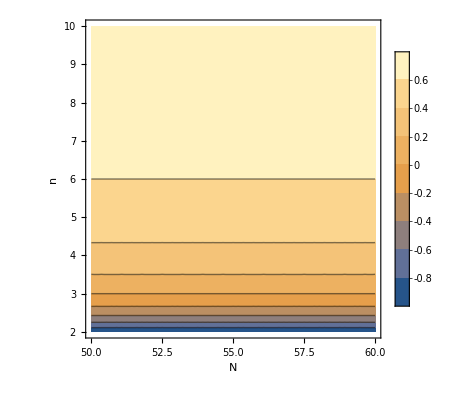

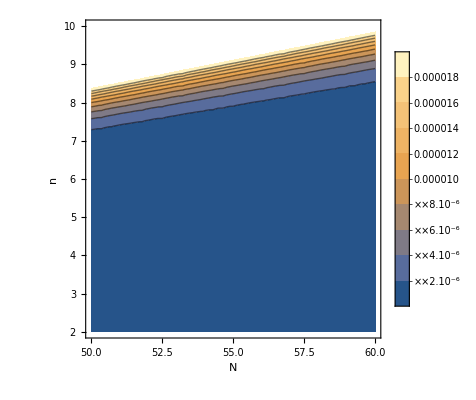

```mathematica
Clear[N0];Clear[n];
ContourPlot[Evaluate[ns[φ]/.φ->φi],{N0,50,60},{n,2,10},FrameLabel->{"N","n"},PlotLegends->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{N0,50,60},{n,2,10},FrameLabel->{"N","n"},PlotLegends->True]
```